```mathematica
FullSimplify[DiscreteAsymptotic[LogGamma[N(1 + α)] - LogGamma[N],N->Infinity]]
```

N α Log[N]

```mathematica
FullSimplify[D[(l +  S)/2,l] Log[(l + S)/(2l)] +
D[(l -  S)/2,l] Log[(l -  S)/(2l)]]
```

1/2 (Log[(l-S)/(4 l)]+Log[(l+S)/l])

```mathematica
LP[s_] :=
Integrate[1/2 (Log[(l-s)/(4 l)]+Log[(l+s)/l]) ,{l,s,1}];
```

```mathematica
FullSimplify[LP[s],{0 <s <1}]
```

s ArcTanh[s]+Log[(√(1-s^2))/2]

```mathematica
(s ArcTanh[s]+Log[(√(1-s^2))/2])/.s->0
```

-Log[2]

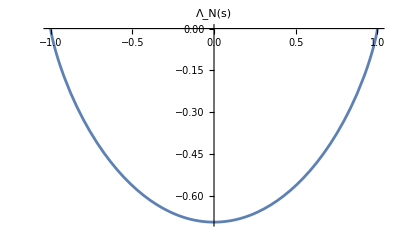

```mathematica
Plot[1/2(1+s) Log[1+s] + 1/2(1-s) Log[1-s] - Log[2],{s,-1,1},PlotLabel->Subscript[Λ,N][s]]
```

```mathematica
FullSimplify[Asymptotic[LogGamma[N+1] - LogGamma[N/2 (1 -s)+1]- LogGamma[N/2 (1 +s)+1],N ->Infinity], N > 2]
```

1/2 N (Log[4]+(-1+s) Log[1-s]-(1+s) Log[1+s])

```mathematica
TrigToExp[s ArcTanh[s]]+1/2 Log[1-s] + 1/2 Log[1+s] - Log[2]//Simplify
```

1/2 (Log[(1-s)/4]-s Log[1-s]+(1+s) Log[1+s])

```mathematica
1/2(1+s) Log[1+s] + 1/2(1-s) Log[1-s] - Log[2]
```

```mathematica
II[ξ_, n_, s_, X_, y_] :=
Block[{α, θ},
α = 2/(y Sqrt[X]);
 Evaluate[2 Pi n(Integrate[θ Exp[2 Pi I n θ ]{Sin[α s], Cos[α s]},{θ,0,s}] + 
Integrate[θ Exp[2 Pi I n θ ]{Sin[α θ], Cos[α θ]},{θ,s,ξ}])//FullSimplify]
];
```

```mathematica
II[ξ,n, s, X, y]
```

{((-1+ⅇ^(2 ⅈ n π s) (1-2 ⅈ n π s)) Sin[(2 s)/(√X y)])/(2 n π)+1/((-4 n^2 π^2+4/(X y^2))^2)2 n π (-ⅇ^(2 ⅈ n π s) ((2 (4 n π (ⅈ+n π s)-(4 s)/(X y^2)) Cos[(2 s)/(√X y)])/(√X y)+(2 n π (2 n π (1-2 ⅈ n π s)+(4 ⅈ s)/(X y^2))+4/(X y^2)) Sin[(2 s)/(√X y)])+ⅇ^(2 ⅈ n π ξ) ((8 ⅈ n π Cos[(2 ξ)/(√X y)])/(√X y)+4 n^2 π^2 Sin[(2 ξ)/(√X y)]+(4 Sin[(2 ξ)/(√X y)])/(X y^2)+(4 n^2 π^2-4/(X y^2)) ξ ((2 Cos[(2 ξ)/(√X y)])/(√X y)-2 ⅈ n π Sin[(2 ξ)/(√X y)]))),((-1+ⅇ^(2 ⅈ n π s) (1-2 ⅈ n π s)) Cos[(2 s)/(√X y)])/(2 n π)+1/((-4 n^2 π^2+4/(X y^2))^2)2 n π (-ⅇ^(2 ⅈ n π s) ((2 n π (2 n π (1-2 ⅈ n π s)+(4 ⅈ s)/(X y^2))+4/(X y^2)) Cos[(2 s)/(√X y)]+(2 (-4 n π (ⅈ+n π s)+(4 s)/(X y^2)) Sin[(2 s)/(√X y)])/(√X y))+ⅇ^(2 ⅈ n π ξ) ((4/(X y^2)+2 n π (2 n π-4 ⅈ n^2 π^2 ξ+(4 ⅈ ξ)/(X y^2))) Cos[(2 ξ)/(√X y)]+(2 (-4 ⅈ n π-4 n^2 π^2 ξ+(4 ξ)/(X y^2)) Sin[(2 ξ)/(√X y)])/(√X y)))}